```mathematica
psi=a{1,0}+b{0,1};
psistar=Conjugate[a]{1,0}+Conjugate[b]{0,1};
rho=KroneckerProduct[psi,psistar]
```

{{a Conjugate[a],a Conjugate[b]},{b Conjugate[a],b Conjugate[b]}}

```mathematica
sigmax={{0,1},{1,0}};
sigmay={{0,-I},{I,0}};
sigmaz={{1,0},{0,-1}};
sigma={sigmax,sigmay,sigmaz};
m={mx,my,mz};
i={{1,0},{0,1}};
Solve[1/2(i+m.sigma)==rho,{mx,my,mz}]
```

{}

```mathematica
Solve[{a*Conjugate[a]==(1+mz)/2,b*Conjugate[b]==(1-mz)/2,(mx+I*my)/2==Conjugate[a]*b,(mx-I*my)/2==Conjugate[b]*a},{mz,my,mz}]
```

{}

```mathematica
sigmay.{{a^2,astar*b},{bstar*a,b^2}}
```

{{-ⅈ a bstar,-ⅈ b^2},{ⅈ a^2,ⅈ astar b}}

```mathematica
$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&;
plus={{1},{1}};
minus={{1},{-1}};
zeroL=KroneckerProduct[{1,1},plus,plus];
oneL=KroneckerProduct[{1,-1},minus,minus];
i={{1,0},{0,1}};
x={{0,1},{1,0}};
z={{1,0},{0,-1}};
```

```mathematica
$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&;
bell={1,0,0,0,0,0,0,1}
KroneckerProduct[i,i,z].bell
```

{1,0,0,0,0,0,0,1}

{1,0,0,0,0,0,0,-1}

```mathematica
zeroL.
```

```mathematica
Simplify[3 p^2(1-p)-3p(1-p)^2-p^3-(1-p)^3]
```

-1+6 p^2-6 p^3

```mathematica
Simplify[3p(1-p)^2-3 p^2(1-p)-p^3-(1-p)^3]
```

-1+6 p-12 p^2+6 p^3

```mathematica
(-1+6 p^2-6 p^3)(-1+6 p-12 p^2+6 p^3)
```

(-1+6 p^2-6 p^3) (-1+6 p-12 p^2+6 p^3)

```mathematica
FullSimplify[(-1+6 p^2-6 p^3) (-1+6 p-12 p^2+6 p^3)]
```

(-1+6 (-1+p)^2 p) (-1-6 (-1+p) p^2)

```mathematica
Expand[(-1+6 (-1+p)^2 p) (-1-6 (-1+p) p^2)]^3
```

(1-6 p+6 p^2+36 p^3-108 p^4+108 p^5-36 p^6)^3

```mathematica
Expand[(1-6 p+6 p^2+36 p^3-108 p^4+108 p^5-36 p^6)^3]
```

1-18 p+126 p^2-324 p^3-864 p^4+8748 p^5-23220 p^6-2592 p^7+181440 p^8-501552 p^9+451008 p^10+839808 p^11-3425328 p^12+5715360 p^13-5855328 p^14+3919104 p^15-1679616 p^16+419904 p^17-46656 p^18

```mathematica
Simplify[1-18 p+126 p^2-324 p^3-864 p^4+8748 p^5-23220 p^6-2592 p^7+181440 p^8-501552 p^9+451008 p^10+839808 p^11-3425328 p^12+5715360 p^13-5855328 p^14+3919104 p^15-1679616 p^16+419904 p^17-46656 p^18]
```

-(-1+6 p-6 p^2-36 p^3+108 p^4-108 p^5+36 p^6)^3

```mathematica
1-18 p+126 p^2-324 p^3-864 p^4+8748 p^5-23220 p^6-2592 p^7+181440 p^8-501552 p^9+451008 p^10+839808 p^11-3425328 p^12+5715360 p^13-5855328 p^14+3919104 p^15-1679616 p^16+419904 p^17-46656 p^18/.p->0.2
```

0.00658716

```mathematica
Ry[theta_]:={{Cos[theta/2],-Sin[theta/2]},{Sin[theta/2],Cos[theta/2]}};
Rx[theta_]:={{Cos[theta/2],-I*Sin[theta/2]},{-I*Sin[theta/2],Cos[theta/2]}};
```

```mathematica
Ry[-π/2]
Rx[π/2]
```

(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2))

(1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2))

```mathematica
{{a^2,a*b},{a*b,b^2}}.{{a^2,I*a*b},{-I*a*b,b^2}}
```

(a^4-ⅈ a^2 b^2 | ⅈ a^3 b+a b^3
a^3 b-ⅈ a b^3 | ⅈ a^2 b^2+b^4)

```mathematica
Y={{1,-I},{I,1}};
Y.{a,b}
```

{a-ⅈ b,ⅈ a+b}

```mathematica
Rx[π].{a,b}
```

{-ⅈ b,-ⅈ a}

```mathematica
Tr[{{a^2,a*b},{a*b,b^2}}.{{a^2,I*a*b},{-I*a*b,b^2}}]
```

a^4+b^4

```mathematica
Eigenvalues[{{a^2,a*b},{a*b,b^2}}-{{a^2,I*a*b},{-I*a*b,b^2}}]
```

{(1+ⅈ) (-1)^(3/4) a b,(-1-ⅈ) (-1)^(3/4) a b}

```mathematica
Solve[Rz[theta].{a,b}=={a,-I*b},{theta}]
```

{}

```mathematica
Rz[theta_]={{Exp[-I*theta/2],0},{0,Exp[I*theta/2]}};
```

```mathematica
Rz[-π/2].{a,b}*Exp[-I*π/4]
```

{a,-ⅈ b}

```mathematica
Exp[I*π/4]
```

ⅇ^((ⅈ π)/4)

```mathematica
N[ⅇ^((ⅈ π)/4)]
```

0.707107+0.707107 ⅈ

```mathematica
(-Omega/2*(Exp[I(we-wg-w)t]-1)/(we-wg-w))(-Omega/2*(Exp[-I(we-wg-w)t]-1)/(we-wg-w))
```

((-1+ⅇ^(-ⅈ t (-w+we-wg))) (-1+ⅇ^(ⅈ t (-w+we-wg))) Omega^2)/(4 (-w+we-wg)^2)

```mathematica
FullSimplify[((-1+ⅇ^(-ⅈ t (-w+we-wg))) (-1+ⅇ^(ⅈ t (-w+we-wg))) Omega^2)/(4 (-w+we-wg)^2)]
```

(Omega^2 Sin[1/2 t (w-we+wg)]^2)/(w-we+wg)^2

```mathematica
(I*deg*epsilon)/(2*hbar)Integrate[Exp[-I*(wg-we)tp]*(Exp[-I*w*tp]+Exp[I*w*tp]),{tp,0,t}]
```

(deg epsilon ((-1+ⅇ^(ⅈ t (w+we-wg)))/(w+we-wg)+(1-ⅇ^(-ⅈ t (w-we+wg)))/(w-we+wg)))/(2 hbar)

```mathematica
Expand[(deg epsilon ((-1+ⅇ^(ⅈ t (w+we-wg)))/(w+we-wg)+(1-ⅇ^(-ⅈ t (w-we+wg)))/(w-we+wg)))/(2 hbar)]
```

-(deg epsilon)/(2 hbar (w+we-wg))+(deg ⅇ^(ⅈ t (w+we-wg)) epsilon)/(2 hbar (w+we-wg))+(deg epsilon)/(2 hbar (w-we+wg))-(deg ⅇ^(-ⅈ t (w-we+wg)) epsilon)/(2 hbar (w-we+wg))

```mathematica
FullSimplify[-(deg epsilon)/(2 hbar (w+we-wg))+(deg ⅇ^(ⅈ t (w+we-wg)) epsilon)/(2 hbar (w+we-wg))+(deg epsilon)/(2 hbar (w-we+wg))-(deg ⅇ^(-ⅈ t (w-we+wg)) epsilon)/(2 hbar (w-we+wg))]
```

(deg ⅇ^(-ⅈ t (w-we+wg)) epsilon ((-1+ⅇ^(2 ⅈ t w)) w-(1+ⅇ^(2 ⅈ t w)-2 ⅇ^(ⅈ t (w-we+wg))) (we-wg)))/(2 hbar (w+we-wg) (w-we+wg))

```mathematica
(-Omega/2(Exp[I*(wq-w)t]/(wq-w)+Exp[I*(wq+w)t]/(wq+w)))(-Omega/2(Exp[-I*(wq-w)t]/(wq-w)+Exp[-I*(wq+w)t]/(wq+w)))
```

1/4 Omega^2 (ⅇ^(-ⅈ t (-w+wq))/(-w+wq)+ⅇ^(-ⅈ t (w+wq))/(w+wq)) (ⅇ^(ⅈ t (-w+wq))/(-w+wq)+ⅇ^(ⅈ t (w+wq))/(w+wq))

```mathematica
FullSimplify[1/4 Omega^2 (ⅇ^(-ⅈ t (-w+wq))/(-w+wq)+ⅇ^(-ⅈ t (w+wq))/(w+wq)) (ⅇ^(ⅈ t (-w+wq))/(-w+wq)+ⅇ^(ⅈ t (w+wq))/(w+wq))]
```

```mathematica
(Omega^2 (w^2+wq^2+(-w^2+wq^2) Cos[2 t w]))/(2 (w^2-wq^2)^2)==(Omega^2 (w^2+wq^2+(-w^2+wq^2) Cos[2 t w]))/(2 (w-wq)^2(w+wq)^2)
```

(Omega^2 (w^2+wq^2+(-w^2+wq^2) Cos[2 t w]))/(2 (w^2-wq^2)^2)==(Omega^2 (w^2+wq^2+(-w^2+wq^2) Cos[2 t w]))/(2 (w-wq)^2 (w+wq)^2)

```mathematica
Reduce[(Omega^2 (w^2+wq^2+(-w^2+wq^2) Cos[2 t w]))/(2 (w^2-wq^2)^2)==]
```

True

```mathematica
(Omega^2 (w^2+wq^2+(-w^2+wq^2)))/(2 (w^2-wq^2)^2)
```

```mathematica
Reduce[(Omega^2 wq^2)/((w^2-wq^2)^2)==(Omega^2 wq^2)/((w-wq)^2(w+wq)^2)]
```

True

```mathematica
Solve[3(1-Exp[-t/T1])-(1-Exp[-t/T1])^3==0.01,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(t→-1.00566 T1
t→0.00333891 T1
t→(0.314188+3.14159 ⅈ) T1)

```mathematica
Log[0.99]
```

-0.0100503

```mathematica
Solve[(1-Exp[-t/T1])==3(1-Exp[-t/T1])-(1-Exp[-t/T1])^3,t]
```

(t→ConditionalExpression[2 ⅈ π T1 C[1], C[1]∈ℤ]
t→ConditionalExpression[T1 (2 ⅈ π C[1]+Log[-1+√2]), C[1]∈ℤ]
t→ConditionalExpression[T1 (ⅈ π+2 ⅈ π C[1]+Log[1+√2]), C[1]∈ℤ])

```mathematica
Perr[t_]:=1-Exp[-t/T1];
```

```mathematica
Solve[0.01==3Perr[t]-3Perr[t]^2+Perr[t]^3,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(t→0.00335011 T1)

```mathematica
FullSimplify[P2err*P1err]
```

(1-p)^3

3 (1-p)^2 p

3 (1-p) p^2

p^3

1-(1-p)^3-3 (1-p)^2 p-p^3

1-(1-p)^3-3 (1-p) p^2-p^3

-9 (-1+p)^3 p^3

```mathematica
Reduce[-3 (-1+p) p^2==3 (1-p)^2 p^2]
```

p==0||p==1

```mathematica
P0=(1-p)^3
P1=3p(1-p)^2
P2=3 p^2(1-p)
P3=p^3
P2err=1-P0-P1-P3
P1err=1-P0-P2-P3
(P2*P1/.p->0.2)^3
(Simplify[P2err*P1err]/.p->0.2)^3
```

(1-p)^3

3 (1-p)^2 p

3 (1-p) p^2

p^3

1-(1-p)^3-3 (1-p)^2 p-p^3

1-(1-p)^3-3 (1-p) p^2-p^3

0.0000500965

0.0000500965

```mathematica
9*9*9
```

729

```mathematica
Simplify[(1-(1-p)^3-3 (1-p)^2 p-p^3) (1-(1-p)^3-3 (1-p)^2 p^2-p^3)]
```

9 (-1+p) p^3 (-1+2 p-2 p^2+p^3)

```mathematica
D[(9 (-1+p) p^3 (-1+2 p-2 p^2+p^3)), p]
```

9 (-1+p) p^3 (2-4 p+3 p^2)+27 (-1+p) p^2 (-1+2 p-2 p^2+p^3)+9 p^3 (-1+2 p-2 p^2+p^3)

```mathematica
Perr[t]
Solve[Perr[t]==3*Perr[t]-3*Perr[t]^2+Perr[t]^3,t]
```

1-ⅇ^(-t/T1)

(t→ConditionalExpression[2 ⅈ π T1 C[1], C[1]∈ℤ]
t→ConditionalExpression[T1 (ⅈ π+2 ⅈ π C[1]), C[1]∈ℤ])

```mathematica
Reduce[3 Perr[t]^2(1-Perr[t])+Perr[t]^3==0.01,t]
Solve[3 Perr[t]^2(1-Perr[t])+Perr[t]^3==Perr[t],t]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&T1≠0&&(t==T1 ((0.697615+3.14159 ⅈ)+(0.+6.28319 ⅈ) C[1])||t==T1 (-0.0551265+(0.+6.28319 ⅈ) C[1])||t==T1 (0.0607092+(0.+6.28319 ⅈ) C[1]))

(t→ConditionalExpression[2 ⅈ π T1 C[1], C[1]∈ℤ]
t→ConditionalExpression[T1 (2 ⅈ π C[1]+Log[2]), C[1]∈ℤ])

```mathematica
Solve[1/E==1-(1-Exp[-t/T1]),t,Reals]
Solve[1/E==1-(3 Perr[t]^2(1-Perr[t])+Perr[t]^3),t,Reals]
```

(t→T1)

(t→T1 Log[Root0.711Root[{2 ⅇ-3 ⅇ #1+#1^3&,0.710682773733645}]0.7106827737336451]
t→T1 Log[Root2.43Root[{2 ⅇ-3 ⅇ #1+#1^3&,2.43321432921916}]2.433214329219163])

```mathematica
N[{{t->T1 Log[Root"0.711"Root[{2 ⅇ-3 ⅇ #1+#1^3&,0.71068277373364513449516266518912743777`15.563227510194512}]0.7106827737336451]}, {t->T1 Log[Root"2.43"Root[{2 ⅇ-3 ⅇ #1+#1^3&,2.43321432921916325220479393465211614966`15.641800131217172}]2.433214329219163]}}]
```

(t→-0.341529 T1
t→0.889213 T1)

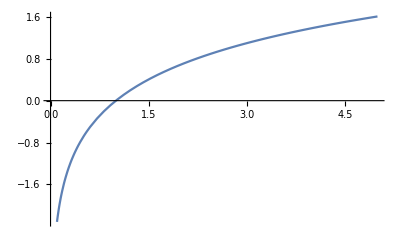

```mathematica
Plot[Log[x],{x,0,5}]
```

```mathematica
Reduce[==(1+2Cos[n*π*√(1+u)])/2]
```

Cos[n π √(1+u)]==1/2 (1-√3)||Cos[n π √(1+u)]==1/2 (1+√3)

∫ⅇ^(-(I0^2 u^2)/(2 sigma^2)) (1/2+1/4 ⅇ^(-2 ⅈ n π √(1-u))+1/4 ⅇ^(2 ⅈ n π √(1-u)))ⅆu

```mathematica
Integrate[ⅇ^(-(I0^2 u^2)/(2 sigma^2)) (1/2),u]
Integrate[ⅇ^(-(I0^2 u^2)/(2 sigma^2))1/4 ⅇ^(-2 ⅈ n π √(1-u)),u]
Integrate[ⅇ^(-(I0^2 u^2)/(2 sigma^2))1/4 ⅇ^(2 ⅈ n π √(1-u)),u]
```

(√(π/2) sigma Erf[(I0 u)/(√2 sigma)])/(2 I0)

1/4 ∫ⅇ^(-2 ⅈ n π √(1-u)-(I0^2 u^2)/(2 sigma^2))ⅆu

1/4 ∫ⅇ^(2 ⅈ n π √(1-u)-(I0^2 u^2)/(2 sigma^2))ⅆu

```mathematica
(*Integrate[Cos[n*π*√(1+u)]^2*Exp[-u^2/(2*sigma^2)I0^2],u]*)
Integrate[(1-(n*π*√(1+u))^2)*Exp[-u^2/(2*sigma^2)I0^2],u]
```

(ⅇ^(-(I0^2 u^2)/(2 sigma^2)) n^2 π^2 sigma^2)/I0^2+(√(π/2) (1-n^2 π^2) sigma Erf[(I0 u)/(√2 sigma)])/I0

```mathematica
NIntegrate[Cos[n*π*√(1+u)]^2*Exp[-u^2/(2*sigma^2)I0^2],{u,
```

NIntegrate::ilim: Invalid integration variable or limit(s) in u.

NIntegrate[Cos[n π √(1+u)]^2 Exp[-(u^2 I0^2)/(2 sigma^2)],u]

```mathematica
Clear["Global`*"]
Series[Cos[n*2*π √(1+x/I0)]^2,{x,0,3}]
Integrate[(1-x-(2 x^2)/3+(43 x^3)/45+(107 x^4)/630)*Exp[-x^2],{x,-∞,∞}];
```

Cos[2 n π]^2+(Cos[2 n π] (-2 n^2 π^2 Cos[2 n π]+n π Sin[2 n π]) x^2)/(2 I0^2)+(Cos[2 n π] (6 n^2 π^2 Cos[2 n π]-3 n π Sin[2 n π]+4 n^3 π^3 Sin[2 n π]) x^3)/(12 I0^3)+O[x]^4

```mathematica
Simplify[(32*n^4*π^4-30*n^2*π^2)/(96 I0^4)]
```

(n^2 π^2 (-15+16 n^2 π^2))/(48 I0^4)

```mathematica
1+(1 (-2 n^2 π^2 1+n π 0) x^2)/(2 I0^2)+(1 (6 n^2 π^2 1-3 n π 0+4 n^3 π^3 0) x^3)/(12 I0^3)+1/(96 I0^4)(-30 n^2 π^2 1^2+32 n^4 π^4 1^2+15 n π 1*0-48 n^3 π^3 1*0+6 n^2 π^2 0^2) x^4
```

1-(n^2 π^2 x^2)/I0^2+(n^2 π^2 x^3)/(2 I0^3)+((-30 n^2 π^2+32 n^4 π^4) x^4)/(96 I0^4)

```mathematica
Simplify[1-(n^2 π^2 x^2)/I0^2+(n^2 π^2 x^3)/(2 I0^3)+((-30 n^2 π^2+32 n^4 π^4) x^4)/(96 I0^4)]
```

1-(n^2 π^2 x^2)/I0^2+(n^2 π^2 x^3)/(2 I0^3)+(n^2 π^2 (-15+16 n^2 π^2) x^4)/(48 I0^4)

```mathematica
1/(√(2π*sigma^2))Integrate[(1-(n^2 π^2 x^2)/I0^2+(n^2 π^2 x^3)/(2 I0^3)+(n^2 π^2 (-15+16 n^2 π^2) x^4)/(48 I0^4))*Exp[-x^2/(2*sigma^2)],{x,-∞,∞}]
```

ConditionalExpression[(√(1/sigma^2) √(sigma^2) (16 I0^4-16 I0^2 n^2 π^2 sigma^2+n^2 π^2 (-15+16 n^2 π^2) sigma^4))/(16 I0^4), Re[sigma^2]>0]

```mathematica
Expand[FullSimplify[1/(16 I0^4) (16 I0^4-16 I0^2 n^2 π^2 sigma^2+n^2 π^2 (-15+16 n^2 π^2) sigma^4)]]
```

```mathematica
P[n_]:=1-(n^2 π^2 sigma^2)/I0^2-(15 n^2 π^2 sigma^4)/(16 I0^4)+(n^4 π^4 sigma^4)/I0^4
P[1]
```

1-(π^2 sigma^2)/I0^2-(15 π^2 sigma^4)/(16 I0^4)+(π^4 sigma^4)/I0^4

```mathematica
Solve[P[n]==1/E,n]
```

(n→-(√(15/π^2+(16 I0^2)/(π^2 sigma^2)-(√(-sigma^4 (-1024 I0^4+768 ⅇ I0^4-480 ⅇ I0^2 sigma^2-225 ⅇ sigma^4)))/(√ⅇ π^2 sigma^4)))/(4 √2)
n→(√(15/π^2+(16 I0^2)/(π^2 sigma^2)-(√(-sigma^4 (-1024 I0^4+768 ⅇ I0^4-480 ⅇ I0^2 sigma^2-225 ⅇ sigma^4)))/(√ⅇ π^2 sigma^4)))/(4 √2)
n→-(√(15/π^2+(16 I0^2)/(π^2 sigma^2)+(√(-sigma^4 (-1024 I0^4+768 ⅇ I0^4-480 ⅇ I0^2 sigma^2-225 ⅇ sigma^4)))/(√ⅇ π^2 sigma^4)))/(4 √2)
n→(√(15/π^2+(16 I0^2)/(π^2 sigma^2)+(√(-sigma^4 (-1024 I0^4+768 ⅇ I0^4-480 ⅇ I0^2 sigma^2-225 ⅇ sigma^4)))/(√ⅇ π^2 sigma^4)))/(4 √2))

```mathematica
P[1]
```

```mathematica
Solve[1-(π^2 sigma^2)/I0^2-(15 π^2 sigma^4)/(16 I0^4)+(π^4 sigma^4)/I0^4==0.99,sigma]
Solve[1-(π^2 sigma^2)/I0^2==0.99,sigma]
```

(sigma→-0.999199
sigma→-0.0959321
sigma→0.0959321
sigma→0.999199)

(sigma→-0.095493
sigma→0.095493)

```mathematica
Solve[1-(n^2 π^2 sigma^2)/I0^2-(15 n^2 π^2 sigma^4)/(16 I0^4)+(n^4 π^4 sigma^4)/I0^4>0.99,]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

({})

```mathematica
P[n]
P[1]
```

1-(n^2 π^2 sigma^2)/I0^2-(15 n^2 π^2 sigma^4)/(16 I0^4)+(n^4 π^4 sigma^4)/I0^4

1-(n^2 π^2 sigma^2)/I0^2-(15 n^2 π^2 sigma^4)/(16 I0^4)+(n^4 π^4 sigma^4)/I0^4

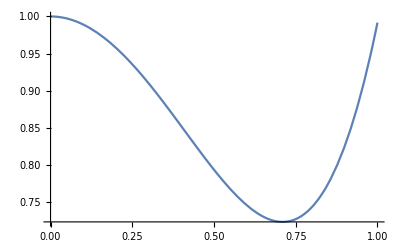

```mathematica
I0=3;
Plot[P[1],{sigma,0,1}]
```

```mathematica
p3[n_]:=1-(1 (-2 n^2 π^2) x^2)/(2 I0^2)+((6 n^2 π^2) x^3)/(12 I0^3)
```

```mathematica
P3[n_]:=1/(√(2π*sigma^2))Integrate[p3[n]*Exp[-x^2/(2*sigma^2)],{x,-∞,∞}]
```

```mathematica
P3[1]
```

ConditionalExpression[(√(1/sigma^2) √(sigma^2) (I0^2+π^2 sigma^2))/I0^2, Re[sigma^2]>0]

```mathematica
Simplify[(I0^2+π^2 sigma^2)/I0^2]
```

```mathematica
Solve[1+(π^2 sigma^2)/I0^2==0.999,sigma]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(sigma→(0.-0.0100658 ⅈ) I0
sigma→(0.+0.0100658 ⅈ) I0)